# ContourPlot

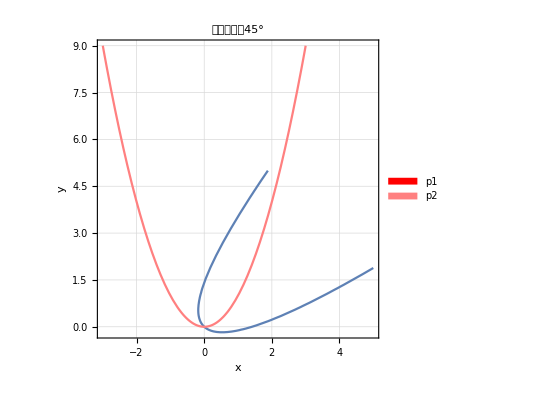

```mathematica
p1=ContourPlot[(x-y)^2==√2(x+y),{x,-1,5},{y,-1,5}];
p2=Plot[x^2,{x,-3,3},PlotStyle->{Pink}];
Legended[
Show[p1,p2,
PlotLabel->"抛物线旋转45°",
PlotRange->Automatic,
GridLines->Automatic,
AxesLabel->{"x","y"}
],
SwatchLegend[{Red,Pink},{"p1","p2"}]

]
```

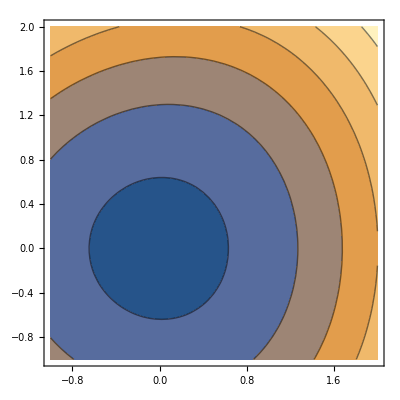

```mathematica
F[x_,y_]:=(x^2+y^2)^4-45 (x^2+y^2)^3-41283 (x^2+y^2)^2+7950960 (x^2+y^2)+16 (x^2-3 y^2)^3+48 (x^2+y^2) (x^2-3 y^2)^2-720^3+(x^2-3 y^2) x (16 (x^2+y^2)^2-5544 (x^2+y^2)+266382);
ContourPlot[F[x,y],{x,-1,2},{y,-1,2}]
```

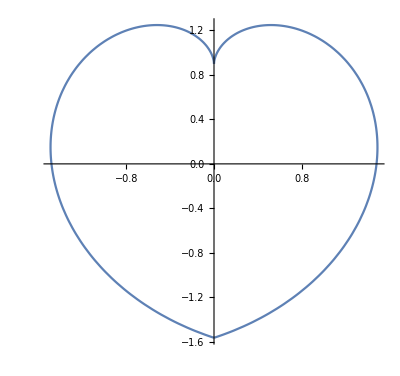

```mathematica
w=Abs[u];
p=w √(w/(1+w));

x=p Sin[u];
y=(p Cos[u] +1) 0.9;
ParametricPlot[{x,y},{u,-π,π}]
```

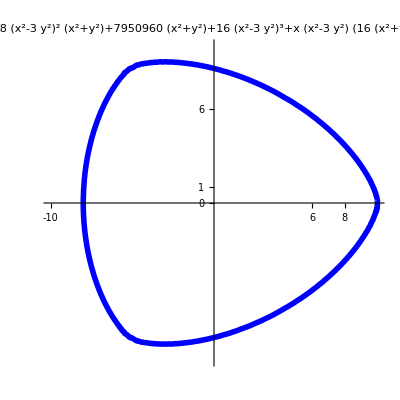

```mathematica
ContourPlot[F[x,y]==0,{x,-10,10},{y,-10,10},ContourStyle->{Blue,Thickness[0.01]},Axes->True,Frame->False,Ticks->{{-10,6,8},{0,1,6}},PlotLabel->F[x,y]==0,AspectRatio->Automatic]
```

```mathematica
ContourPlot3D[x^x+y^y+z^z==2.3,{x,0,1.1},{y,0,1.1},{z,0,1.1},
Axes->False,
PlotLabel->Style["怎么能把外框去掉",Red,30],
MeshStyle->Dashed,
Mesh->5,
ColorFunction->Function[{x,y,z},Hue[x+y+z]]
]
```

-Graphics3D-

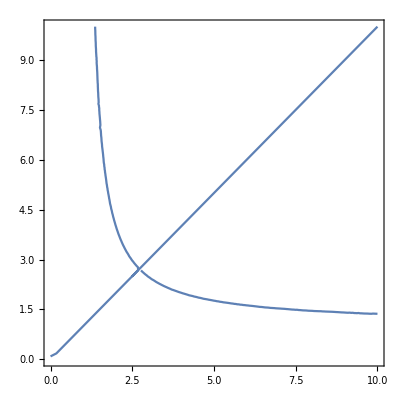

```mathematica
ContourPlot[x^y==y^x,{x,0,10},{y,0,10}]
```